## (a)Analytical solution of the equation

```mathematica
(*Using mathematica's function to directly solve.*)
v=2
DSolve[{r''[x]+r'[x]/x+(1-v^2/x^2)*r[x]==0,r[1]==0,r[0.1]==1},r[x],x]
```

2

{{r[x]→-0.112561 BesselJ[2,x]-0.00783534 BesselY[2,x]}}

```mathematica
{{r[x]->-0.11256110682996633 BesselJ[2,x]-0.007835342414797 BesselY[2,x]}}⟦1,1,2⟧
```

-0.112561 BesselJ[2,x]-0.00783534 BesselY[2,x]

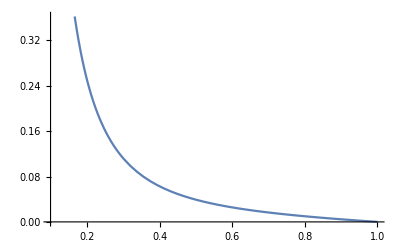

```mathematica
(*Obviously the analytical solution is in the form of Bessel functions. Next draw the graph.*)
Plot[-0.11256110682996633 BesselJ[2,x]-0.007835342414797 BesselY[2,x],{x,0.1,1}]
```

## (b)Numerical solution of the equation

```mathematica
(*Using mathematica's numerically slove function.*)
v=2;
NDSolve[{r''[x]+r'[x]/x+(1-v^2/x^2)*r[x]==0,r[1]==0,r[0.1]==1},r[x],x]
```

{{r[x]→InterpolatingFunction[…][x]}}

```mathematica
%9⟦1,1,2⟧
```

InterpolatingFunction[…][x]

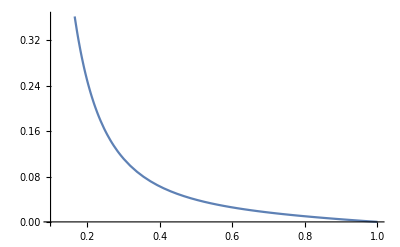

```mathematica
(*This is an approximate function derived from the difference method. Next draw the graph*)
Plot[%10,{x,0.1,1.}]
```

```mathematica
(*The graphs of the two functions are very similar,indicating that the numerical solution is also accurate*)
```